```mathematica
Exit[]
```

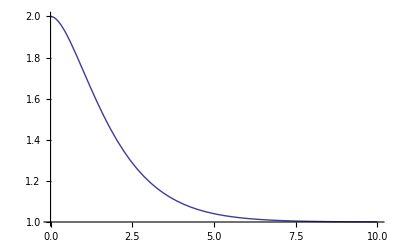

```mathematica
tend=10;
k=1;
lo=1;
Fe=Function[x,Module[{d},
d=-x/Abs[x];
k(x-lo)d
]];
mu=2;
Fd=Function[v,-mu*v];
eq={x1[0]==2,x1'[0]==0,x1''[t]==Fe[x1[t]]+Fd[x1'[t]]};
sol=NDSolve[eq,x1,{t,0,tend}];
Plot[x1[t]/.sol,{t,0,tend},PlotRange->All]
```

```mathematica
a=Function[{t,x,v},Fe[x]+Fd[v]]
```

Function[{t,x,v},Fe[x]+Fd[v]]

```mathematica
f=Function[dat,
{t0,x0,v0}=dat;
ti=t0+dt/2.;
viSol=Solve[vi==v0+0.5*dt*a[ti,x0,vi]][[1]];
x1=x0+dt*vi/.viSol;
xi=(x0+x1)/2.;
viSol=Solve[vi==v0+0.5*dt*a[ti,xi,vi]][[1]];
v1=2*vi-v0/.viSol;
t1=t0+dt;
{t1,x1,v1}
];
```

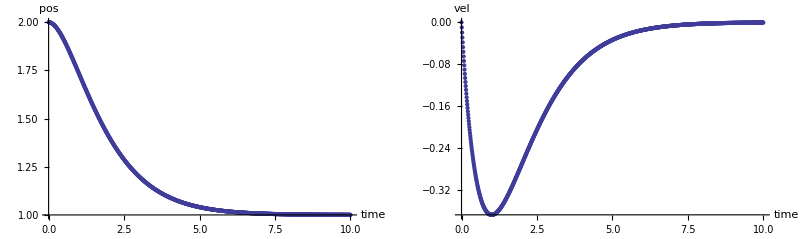

```mathematica
dt=.01;
dat=NestList[f,{0.,2,0},Ceiling[tend/dt]];
GraphicsRow[{Show[
Plot[x1[t]/.sol,{t,0,tend},PlotRange->All,AxesLabel->{"time","pos"}],
ListPlot[dat[[All,{1,2}]]]],
ListPlot[dat[[All,{1,3}]],AxesLabel->{"time","vel"}]},ImageSize->Full]
```

```mathematica
dat=Function[dt,
dat=NestList[f,{0.,2,0},Ceiling[tend/dt]];
{dt,Mean@Abs[dat[[All,2]]-(x1[t]/.sol[[1]]/.t->dat[[All,1]])]}
]/@{0.01,0.02,0.1,0.3,1.0}
```

{{0.01,5.11985×10^-6},{0.02,8.10294×10^-6},{0.1,1.47998×10^-6},{0.3,1.60479×10^-6},{1.,7.17116×10^-7}}

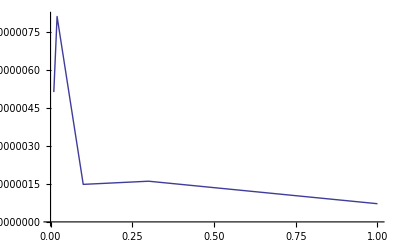

```mathematica
ListLinePlot[dat]
```

```mathematica
dt=.1;
f=Function[dat,
{t0,x0,v0}=dat;
vi=Solve[vi==v0+0.5*dt*a[x0,v1]][[1,1,2]];
x1=x0+dt*vi;
{x1,v0}=Collision[x0,x1,v0];
xi=(x0+x1)/2.;
vi=.;
vi=Solve[vi==v0+0.5*dt*a[xi,vi]][[1,1,2]];
v1=2*vi-v0;
t1=t0+dt;
{t1,x1,v1}
];
```

```mathematica
f[{0,2,0}]
```

```mathematica
Collision=Function[{x0,x1,vi},Module[{o=0.5,Ic},
If[x1<o,
If[vi<0,
Ic=vi/2.;{o,vi-Ic},
{o,vi}],
{x1,vi}
]
]];
dat=NestList[f,{0.,2,0},Ceiling[10/dt]];
DisplayTogether[
Plot[x1[t]/.sol,{t,0,tend},PlotRange->All],
ListPlot[dat[[All,{1,2}]]]];
ListPlot[dat[[All,{1,3}]]];
```

```mathematica
k=1;
lo=1;
Fe=Function[x,Module[{d},
d=-x/Norm[x];
k(Norm[x]-lo)d
]];
mu=1;
Fd=Function[v,-mu*v];
eq=Join[{x1[0]==2,x2[0]==2,x1'[0]==0,x2'[0]==0},Thread[{x1''[t],x2''[t]}==Fe[{x1[t],x2[t]}]+Fd[{x1'[t],x2'[t]}]]];
sol=NDSolve[eq,{x1,x2},{t,0,10}];
ParametricPlot[{x1[t],x2[t]}/.sol,{t,0,10}];
```

```mathematica
{x1[t],x2[t]}/.sol[[1]]/.t->Range[10]//Transpose
```

{{1.56003,1.56003},{0.901783,0.901783},{0.546329,0.546329},{0.509135,0.509135},{0.610669,0.610669},{0.704147,0.704147},{0.740258,0.740258},{0.734249,0.734249},{0.716242,0.716242},{0.704301,0.704301}}

```mathematica
Plot[{x1[t],x2[t]}/.sol[[1]]//Evaluate,{t,0,10}]
```

⁃Graphics⁃

## spring-damper model

```mathematica
k=1;
μ=1;
F=Function[{x0,x1,v0,v1},
u=x1-x0;
un=u/Norm[u];
(k(Norm[u]-1)+μ(v1-v0).un)un
];
F[{2,2},{1,1},{0,0},{0,0.}]
```

{-0.292893,-0.292893}